### Srinivas’s interpretation of Nagel’s model

```mathematica
par = {ka->0.1, sa->10,kb->1,sb->100,θ->10,ko->500,kc->10,α->0.8,β->0.6};
```

```mathematica
R'[t]==-R[t](ka sa+O[t]kb sb)+RX[t]sa+sb(1-R[t]-RX[t]-ORX[t]);
RX'[t]==-R[t](ka sa)-RX[t](sa+O[t] θ kb sb)+ORX[t]sb;
ORX'[t]==RX[t]O[t] θ kb sb+(1-R[t]-RX[t]-ORX[t])θ ka sa-ORX[t](sa+sb);
C'[t]==ko/D[t](RX[t]+ORX[t])(1-C[t])-kc C[t];
D'[t]==α C[t]-β D[t];
```

initial conditions

```mathematica
R[0]==0.1;RX[0]==0.1; ORX[0]==0.1; OR[0]==0.1;
```

THERE ARE 2 ERRORS: 
    - the first rate for RX’[t] is PLUS R[t](Ka sa) not minus
    - the initial condition cannot be 0.1 for all receptor states since then their sum is not 1. In other words in this case total amount of receptor is 0.4.

### corrected reduced model

first we define the equations, initial conditions and signal.

```mathematica
eq={
R'[t]    ==  -ka sa R[t]  +sa RX[t]  -   kb sb OO[t] R[t]  +sb (1-R[t]-RX[t]-ORX[t]),
RX'[t]  ==    ka sa R[t]  -sa RX[t]  -θ kb sb OO[t] RX[t]+sb ORX[t],ORX'[t]==θ ka sa (1-R[t]-RX[t]-ORX[t])-sa ORX[t]+θ kb sb OO[t] RX[t]-sb ORX[t],
CC'[t]==ko/DD[t](RX[t]+ORX[t])(1-CC[t])-kc CC[t],
       DD'[t]==α CC[t]-β DD[t]};
init = {R[0]==Subscript[R, 0],RX[0]==Subscript[RX, 0],ORX[0]==Subscript[ORX, 0],CC[0]==Subscript[CC, 0],DD[0]==Subscript[DD, 0]};
Step[t_,t0_,τ_]=(Tanh[(t-t0)/τ]+1)/2;
Pulse[t_,t0_,tlen_,τ_]=Step[t,t0,τ](1-Step[t,t0+tlen,τ]);
Signal[t_,Sbackground_,Samplitude_,tStart_,tDuration_,tSharp_]=Sbackground +Samplitude Pulse[t,tStart,tDuration,tSharp];
```

test the signal function

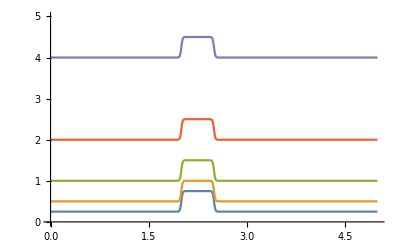

```mathematica
Plot[Evaluate[Table[Signal[t,S0,0.5,2,0.5,0.02],{S0,{0.25,0.5,1,2,4}}]],{t,0,5},PlotRange->{All,{0,5}}]
```

now we solve the differential equation telling the solver to use Sbackground and Samplitude as parameters

```mathematica
par = {ka->0.1, sa->10,kb->1,sb->100,θ->10,ko->500,kc->10,α->0.8,β->0.6,Subscript[R, 0]->1,Subscript[RX, 0]->0,Subscript[ORX, 0]->0,Subscript[CC, 0]->0.4,Subscript[DD, 0]->0.4,tStart->20,tDuration->0.5,tSharp->0.02,tMax->30};
eqs=Join[eq,init]/.par/.OO[t]->Signal[t,Sbackground,Samplitude,tStart,tDuration,tSharp]/.par;
sol=ParametricNDSolveValue[eqs,{R,RX,ORX,CC,DD},{t,0,(tMax/.par)},{Sbackground,Samplitude},Method->"StiffnessSwitching",MaxSteps->10^6];
```

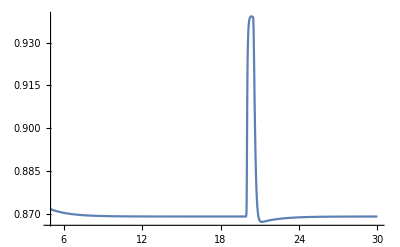

```mathematica
Plot[sol[0.1,1][[4]][t],{t,5,tMax/.par},PlotRange->All]
```

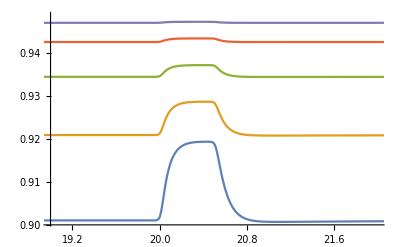

```mathematica
Plot[Evaluate[Table[sol[S0,0.2][[4]][t],{S0,{0.25,0.5,1,2,4}}]],{t,5,tMax/.par},PlotRange->{{19,22},All}]
```

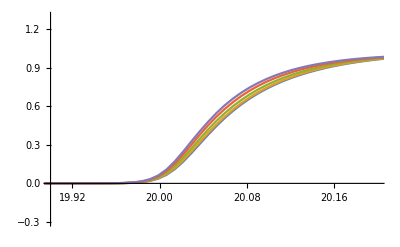

```mathematica
Plot[Evaluate[Table[(sol[S0,0.2][[4]][t]-sol[S0,0.2][[4]][19.8])/(sol[S0,0.2][[4]][20.25]-sol[S0,0.2][[4]][19.8]),{S0,{0.25,0.5,1,2,4}}]],{t,5,tMax/.par},PlotRange->{{19.9,20.2},{-0.3,1.3}}]
```

It looks like the response becomes faster as the system is adapted to a higher background... Contrary from what we see.

### corrected reduced model but make DD multiply both rates

first we define the equations, initial conditions and signal.

```mathematica
eq={
R'[t]    ==  -ka sa R[t]  +sa RX[t]  -   kb sb OO[t] R[t]  +sb (1-R[t]-RX[t]-ORX[t]),
RX'[t]  ==    ka sa R[t]  -sa RX[t]  -θ kb sb OO[t] RX[t]+sb ORX[t],ORX'[t]==θ ka sa (1-R[t]-RX[t]-ORX[t])-sa ORX[t]+θ kb sb OO[t] RX[t]-sb ORX[t],
DD[t]CC'[t]==ko(RX[t]+ORX[t])(1-CC[t])-kc CC[t],
       DD'[t]==α CC[t]-β DD[t]};
init = {R[0]==Subscript[R, 0],RX[0]==Subscript[RX, 0],ORX[0]==Subscript[ORX, 0],CC[0]==Subscript[CC, 0],DD[0]==Subscript[DD, 0]};
Step[t_,t0_,τ_]=(Tanh[(t-t0)/τ]+1)/2;
Pulse[t_,t0_,tlen_,τ_]=Step[t,t0,τ](1-Step[t,t0+tlen,τ]);
Signal[t_,Sbackground_,Samplitude_,tStart_,tDuration_,tSharp_]=Sbackground +Samplitude Pulse[t,tStart,tDuration,tSharp];
```

test the signal function

```mathematica
Plot[Evaluate[Table[Signal[t,S0,0.5,2,0.5,0.02],{S0,{0.25,0.5,1,2,4}}]],{t,0,5},PlotRange->{All,{0,5}}]
```

-Graphics-

now we solve the differential equation telling the solver to use Sbackground and Samplitude as parameters

```mathematica
par = {ka->0.1, sa->10,kb->1,sb->100,θ->10,ko->50,kc->10,α->0.8,β->0.6,Subscript[R, 0]->1,Subscript[RX, 0]->0,Subscript[ORX, 0]->0,Subscript[CC, 0]->0.4,Subscript[DD, 0]->0.1,tStart->20,tDuration->0.5,tSharp->0.02,tMax->30};
eqs=Join[eq,init]/.par/.OO[t]->Signal[t,Sbackground,Samplitude,tStart,tDuration,tSharp]/.par;
sol=ParametricNDSolveValue[eqs,{R,RX,ORX,CC,DD},{t,0,(tMax/.par)},{Sbackground,Samplitude},Method->"StiffnessSwitching",MaxSteps->10^6];
```

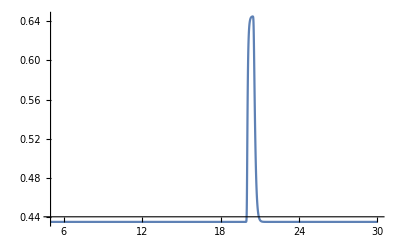

```mathematica
Plot[sol[0.1,1][[4]][t],{t,5,tMax/.par},PlotRange->All]
```

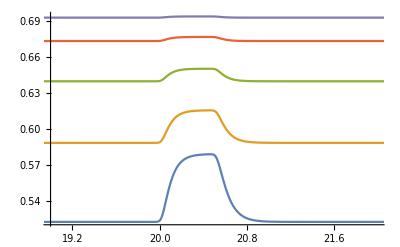

```mathematica
Plot[Evaluate[Table[sol[S0,0.2][[4]][t],{S0,{0.25,0.5,1,2,4}}]],{t,5,tMax/.par},PlotRange->{{19,22},All}]
```

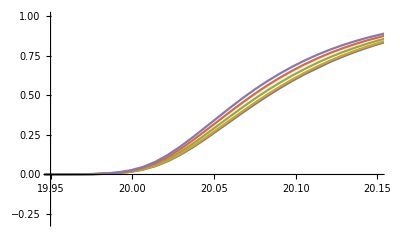

```mathematica
Plot[Evaluate[Table[(sol[S0,0.2][[4]][t]-sol[S0,0.2][[4]][19.8])/(sol[S0,0.2][[4]][20.25]-sol[S0,0.2][[4]][19.8]),{S0,{0.25,0.5,1,2,4}}]],{t,5,tMax/.par},PlotRange->{{19.95,20.15},{-0.3,1.}}]
```

It looks like the response becomes faster as the system is adapted to a higher background... Contrary from what we see.

### corrected reduced model with adiabatic approximations for the conformation changes

first we define the equations, initial conditions and signal.

```mathematica
adiabatic = Solve[{R[t]==RX[t]/ka,
1-R[t]-RX[t]-ORX[t]==ORX[t]/(θ ka),
0==  θ kb sb OO[t] RX[t]-sb ORX[t]},{R[t],RX[t],ORX[t]}][[1]]//Simplify
```

{R[t]→1/(1+ka+(kb+ka kb θ) OO[t]),RX[t]→ka/(1+ka+(kb+ka kb θ) OO[t]),ORX[t]→(ka kb θ OO[t])/(1+ka+(kb+ka kb θ) OO[t])}

```mathematica
FullSimplify[RX[t]+ORX[t]/.adiabatic]
```

(ka+ka kb θ OO[t])/(1+ka+(kb+ka kb θ) OO[t])

```mathematica
(1+kb θ OO[t])/((1+ka)/ka+(kb+ka kb θ)/ka OO[t])
```

```mathematica
eq={
CC'[t]==ko/DD[t]((ka+ka kb θ OO[t])/(1+ka+(kb+ka kb θ) OO[t]))(1-CC[t])-kc CC[t],
       DD'[t]==α CC[t]-β DD[t]};
init = {CC[0]==Subscript[CC, 0],DD[0]==Subscript[DD, 0]};
```

now we solve the differential equation telling the solver to use Sbackground and Samplitude as parameters

```mathematica
par = {ka->0.1, sa->10,kb->1,sb->100,θ->10,ko->500,kc->10,α->0.8,β->0.6,Subscript[R, 0]->1,Subscript[RX, 0]->0,Subscript[ORX, 0]->0,Subscript[CC, 0]->0.4,Subscript[DD, 0]->0.4,tStart->20,tDuration->0.5,tSharp->0.02,tMax->30};
eqs=Join[eq,init]/.par/.OO[t]->Signal[t,Sbackground,Samplitude,tStart,tDuration,tSharp]/.par;
sol=ParametricNDSolveValue[eqs,{CC,DD},{t,0,(tMax/.par)},{Sbackground,Samplitude},Method->"StiffnessSwitching",MaxSteps->10^6];
```

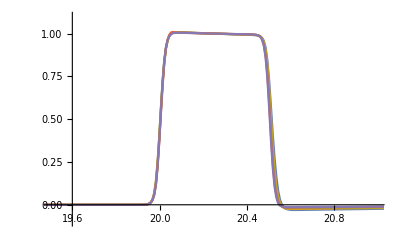

```mathematica
Plot[Evaluate[Table[(sol[S0,0.2][[1]][t]-sol[S0,0.2][[1]][19.8])/(sol[S0,0.2][[1]][20.25]-sol[S0,0.2][[1]][19.8]),{S0,{0.125,0.25,0.5,1,2}}]],{t,5,tMax/.par},PlotRange->{{19.5,21},{-0.1,1.1}}]
```

### corrected reduced model with adiabatic approximations for the conformation changes and DD multiplying both rates

first we define the equations, initial conditions and signal.

```mathematica
adiabatic = Solve[{R[t]==RX[t]/ka,
1-R[t]-RX[t]-ORX[t]==ORX[t]/(θ ka),
0==  θ kb sb OO[t] RX[t]-sb ORX[t]},{R[t],RX[t],ORX[t]}][[1]]//Simplify
```

{R[t]→1/(1+ka+(kb+ka kb θ) OO[t]),RX[t]→ka/(1+ka+(kb+ka kb θ) OO[t]),ORX[t]→(ka kb θ OO[t])/(1+ka+(kb+ka kb θ) OO[t])}

```mathematica
FullSimplify[RX[t]+ORX[t]/.adiabatic]
```

(ka+ka kb θ OO[t])/(1+ka+(kb+ka kb θ) OO[t])

```mathematica
(1+kb θ OO[t])/((1+ka)/ka+(kb+ka kb θ)/ka OO[t])
```

```mathematica
FullSimplify[(1+ka+(kb+ka kb θ) OO[t] )/ (ka kb θ OO[t])]
```

(1+ka+(kb+ka kb θ) OO[t])/(ka kb θ OO[t])

```mathematica
eq={
DD[t]CC'[t]==ko((ka+ka kb θ OO[t])/(1+ka+(kb+ka kb θ) OO[t]))(1-CC[t])-kc CC[t],
       DD'[t]==α CC[t]-β DD[t]};
init = {CC[0]==Subscript[CC, 0],DD[0]==Subscript[DD, 0]};
```

now we solve the differential equation telling the solver to use Sbackground and Samplitude as parameters

```mathematica
par = {ka->0.1, sa->10,kb->1,sb->100,θ->10,ko->50,kc->5 10,α->100 0.8,β->10 0.6,Subscript[R, 0]->1,Subscript[RX, 0]->0,Subscript[ORX, 0]->0,Subscript[CC, 0]->0.4,Subscript[DD, 0]->0.4,tStart->20,tDuration->0.5,tSharp->0.02,tMax->30};
eqs=Join[eq,init]/.par/.OO[t]->0.1Signal[t,Sbackground,Samplitude,tStart,tDuration,tSharp]/.par;
sol=ParametricNDSolveValue[eqs,{CC,DD},{t,0,(tMax/.par)},{Sbackground,Samplitude},Method->"StiffnessSwitching",MaxSteps->10^6];
```

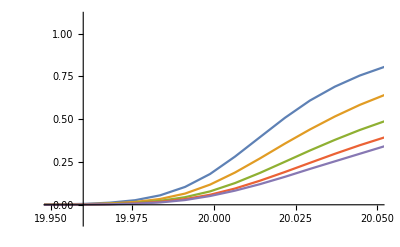

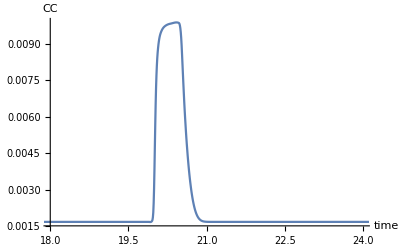

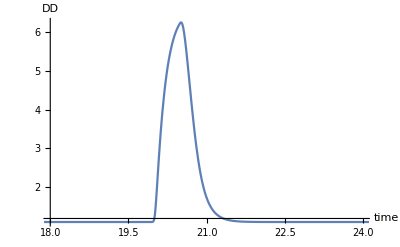

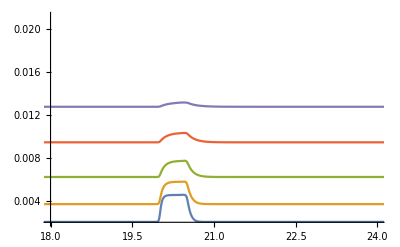

-Graphics-

-Graphics-

```mathematica
Plot[Evaluate[Table[(sol[S0,0.2][[1]][t]-sol[S0,0.2][[1]][19.8])/(sol[S0,0.2][[1]][20.25]-sol[S0,0.2][[1]][19.8]),{S0,{0.125,0.25,0.5,1,2}}]],{t,5,tMax/.par},PlotRange->{{19.95,20.05},{-0.1,1.1}}]
Plot[sol[0.1,1][[1]][t],{t,5,tMax/.par},PlotRange->{{18,24},All},AxesLabel->{"time","CC"}]
Plot[sol[0.1,1][[2]][t],{t,5,tMax/.par},PlotRange->{{18,24},All},AxesLabel->{"time","DD"}]
```

### even simpler

first we define the equations, initial conditions and signal.

```mathematica
eq={
DD[t]CC'[t]==(1/(1+Kd/OO[t]))(1-CC[t])-kc CC[t],
       DD'[t]==α CC[t]-β DD[t]};
init = {CC[0]==Subscript[CC, 0],DD[0]==Subscript[DD, 0]};
```

now we solve the differential equation telling the solver to use Sbackground and Samplitude as parameters

```mathematica
par = {Kd->0.11,kc->5 10,α->5000 0.8,β->10 0.6,Subscript[R, 0]->1,Subscript[RX, 0]->0,Subscript[ORX, 0]->0,Subscript[CC, 0]->0.4,Subscript[DD, 0]->0.4,tStart->20,tDuration->0.5,tSharp->0.02,tMax->30};
eqs=Join[eq,init]/.par/.OO[t]->0.1Signal[t,Sbackground,Samplitude,tStart,tDuration,tSharp]/.par;
sol=ParametricNDSolveValue[eqs,{CC,DD},{t,0,(tMax/.par)},{Sbackground,Samplitude},Method->"StiffnessSwitching",MaxSteps->10^6];
```

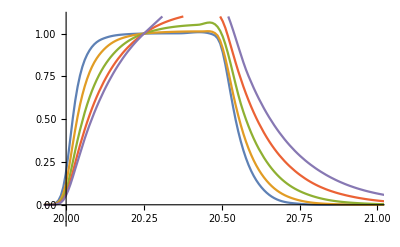

-Graphics-

-Graphics-

-Graphics-

```mathematica
Plot[Evaluate[Table[(sol[S0,0.2][[1]][t]-sol[S0,0.2][[1]][19.8])/(sol[S0,0.2][[1]][20.25]-sol[S0,0.2][[1]][19.8]),{S0,{0.125,0.25,0.5,1,2}}]],{t,5,tMax/.par},PlotRange->{{19.95,21},{-0.1,1.1}}]
Plot[Evaluate[Table[sol[S0,0.2][[1]][t],{S0,{0.125,0.25,0.5,1,2}}]],{t,5,tMax/.par},PlotRange->{{18,24},All}]
Plot[sol[0.1,1][[1]][t],{t,5,tMax/.par},PlotRange->{{18,24},All},AxesLabel->{"time","CC"}]
Plot[sol[0.1,1][[2]][t],{t,5,tMax/.par},PlotRange->{{18,24},{0,1}},AxesLabel->{"time","DD"}]
```